{1.,0.}

{0.0147783,0.00492611}

{0.00744417,0.00496278}

{0.00497512,0.00497512}

0.25

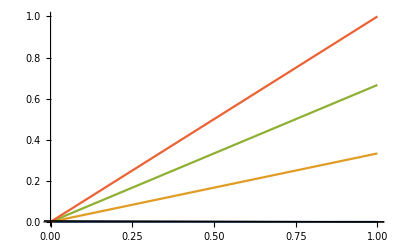

```mathematica
l1=Plot[{0,1/3x,2/3x,x},{x,0,1}];
p=0.005;
fun=InfiniteLine[{{1,0},{0,p}}];
l2=Graphics[InfiniteLine[{{1,0},{0,p}}]];
a=NSolve[{x,y}∈fun&&y==0&&x>0,{x,y}];
b=NSolve[{x,y}∈fun&&y==1/3x&&x>0,{x,y}];
c=NSolve[{x,y}∈fun&&y==2/3x&&x>0,{x,y}];
d=NSolve[{x,y}∈fun&&y==x&&x>0,{x,y}];

a={a[[1,1,2]],a[[1,2,2]]}
b={b[[1,1,2]],b[[1,2,2]]}
c={c[[1,1,2]],c[[1,2,2]]}
d={d[[1,1,2]],d[[1,2,2]]}
ratio=(EuclideanDistance[a,b]/EuclideanDistance[b,d])/(
EuclideanDistance[a,c]/EuclideanDistance[c,d])
Show[{l1,l2}]
```